```mathematica
ClearAll["Global`*"]
```

```mathematica
E1x[n_,k_,b_]:=Sum[ Binomial[k,j2] E2a[n,k-j2,b],{j2,0,k}]
DDx[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j E1x[n/b^j, k, b],{j,0,Log[b,n]}]
D2x[n_,k_,b_]:=Sum[(-1)^j Binomial[k,j] DDx[n,k-j,b],{j,0,k}]

E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
E1a[n_,k_, a_]:= E1a[n,k,a]=Sum[ E1a[n/j,k-1,a],{j,1,n}]-a Sum[ E1a[n/(a j),k-1,a],{j,1,n/a}];E1a[n_,0,a_]:=1

DDa[n_,k_]:=DDa[n,k]=Sum[MoebiusMu[j]DDa[Floor[n/j],k-1],{j,1,n}];DDa[n_,0]:=1
D2a[n_,k_]:=D2a[n,k]=Sum[MoebiusMu[j]D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1

D2b[n_,k_]:=Sum[(-1)^j Binomial[k,j] DDa[n,k-j],{j,0,k}]
DDb[n_,k_]:=Sum[Binomial[k,j] D2a[n,k-j],{j,0,k}]
E2b[n_,k_,b_]:=Sum[(-1)^j Binomial[k,j] E1a[n,k-j,b],{j,0,k}]
E1b[n_,k_,b_]:=Sum[ Binomial[k,j] E2a[n,k-j,b],{j,0,k}]

DDd[n_,z_]:=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]

DDc[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j E1a[n/b^j, k, b],{j,0,Log[b,n]}]
E1c[n_,k_,b_]:=Sum[(-1)^j Binomial[k,j] b^j DDa[n/b^j,k],{j,0,k}]
E2c[n_,k_,b_]:=Sum[(-1)^j b^j Binomial[k,j] Binomial[j,m]D2a[n/b^j,k-m],{j,0,k},{m,0,j}]
D2E2[n_,k_,b_]:= Sum[ (-1)^j b^j Binomial[k,j] Sum[ Binomial[j,m] If[n/b^j<1,0,D2a[n/b^j,k-m]],{m,0,j}],{j,0,k}]
E2D2[n_,k_,b_]:= (-1)^k+Sum[b^a/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[b^-a n,j,b],{a,0,Log[b,n]},{j,0,k}]
```

```mathematica
{DDa[nn=100,aa=2],DDb[nn,aa],DDd[nn,aa]}
```

{19,19,19}

```mathematica
{D2a[nn=100,aa=3],D2b[nn,aa]}
```

{-8,-8}

```mathematica
f1[n_,a_] := Sum[ MoebiusMu[a j],{j,1,n}]
```

```mathematica
f2[n_] := Sum[ (-1)^(j+1) MoebiusMu[j],{j,1,n}]
```

```mathematica
f1[100,1]
```

1

```mathematica
f2[100]
```

-15

```mathematica
f3[n_] := f1[n,1]-2f1[n/2,2]
```

```mathematica
f3[100]
```

-15

```mathematica
f4[n_,a_,c_]:= Sum[ (MoebiusMu[Floor[a j]]),{j,1,n}]-c Sum[MoebiusMu[Floor[a c j]],{j,1,n/c}]
f4a[n_,s_]:=Sum[ s^k f4[n/(s^k),s^k,s],{k,0,Log[s,n]}]
```

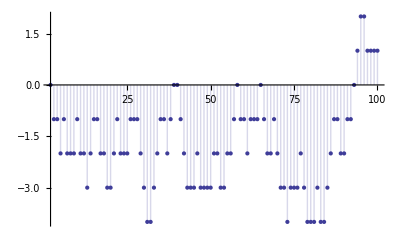

```mathematica
DiscretePlot[f4a[n,2.1],{n,2,100}]
```

```mathematica
ref[n_,k_] := Sum[ (-1)^(j+1)MoebiusMu[j]ref[Floor[n/j],k-1],{j,2,n}];ref[n_,0]:=1
tt[n_,k_]:=Mod[n,k]-Mod[n-1,k]

ref2[n_,k_,a_]:=Sum[ tt[j,a]MoebiusMu[j]ref2[Floor[n/j],k-1,a],{j,2,n}];ref2[n_,0,a_]:=1
```

```mathematica
ref2a[n_,k_,a_]:=Sum[ tt[j,a]MoebiusMu[j]ref2a[Floor[n/j],k-1,a],{j,1,n}];ref2a[n_,0,a_]:=1
```

```mathematica
ref7[n_,k_,a_,c_]:=ref7[n,k,a,c]=
Sum[ MoebiusMu[Floor[a j]]ref7[Floor[n/j],k-1,a,c],{j,2,n}]-c Sum[MoebiusMu[Floor[a j c]]ref7[Floor[n/(j c)],k-1,a,c],{j,1,n/c}];ref7[n_,0,a_,c_]:=1
```

```mathematica
ref8[n_,k_,a_,c_]:=
Sum[ MoebiusMu[Floor[a j]]ref8[Floor[n/j],k-1,a,c],{j,1,n}]-c Sum[MoebiusMu[Floor[a j c]]ref8[Floor[n/(j c)],k-1,a,c],{j,1,n/c}];ref8[n_,0,a_,c_]:=1
ref8a[n_,s_]:=Sum[ s^k ref8[n/(s^k),1,s^k,s],{k,0,Log[s,n]}]
ref8b[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j ref8[n/b^j, k, b^j,b],{j,0,Log[b,n]}]

test[n_, z_] := Sum[FactorialPower[z,a]/a! ref[n,a],{a,0,Log[2,n]}]
test2[n_, z_,s_] := Sum[FactorialPower[z,a]/a! ref2[n,a,s],{a,0,Log[2,n]}]
test3[n_, z_,s_] := Sum[FactorialPower[z,a]/a! ref7[n,a,1,s],{a,0,Log[2,n]}]
linm[n_,s_]:=Sum[ (-1)^(k)/k ref7[n,k,1,s],{k,1,Log[If[s<2,s,2],n]}]
```

```mathematica
{ref2[1200,3,7],ref7[1200,3,1,7]}
```

{-1840,-1840}

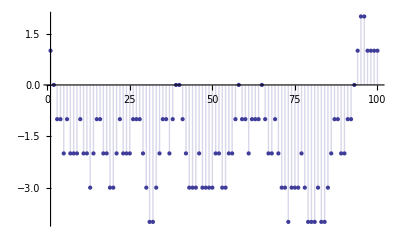

```mathematica
DiscretePlot[ref8a[n,1.2],{n,1,100}]
```

```mathematica
DiscretePlot[ref8b[n,1,2],{n,1,100}]
```

-Graphics-

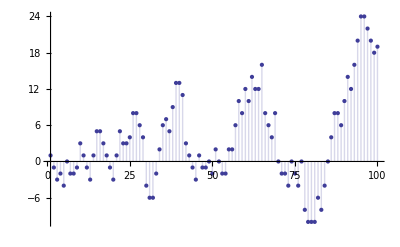

```mathematica
DiscretePlot[DDa[n,2],{n,1,100}]
```

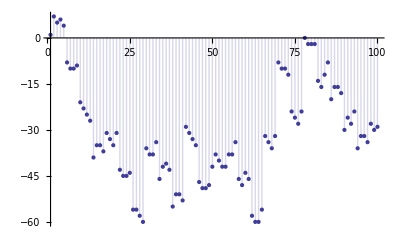

```mathematica
DiscretePlot[ref8b[n,2,2],{n,1,100}]
```

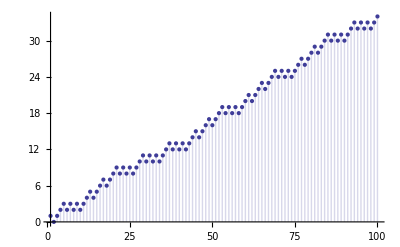

```mathematica
DiscretePlot[test3[n,-1,2],{n,1,100}]
```

```mathematica
pp[n_] := pp[n]=Sum[ MangoldtLambda[j]/Log[j],{j,2,n}]
```

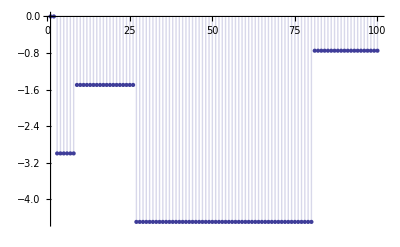

```mathematica
DiscretePlot[linm[n,3],{n,1,100}]
```